-Graphics-

# Probability and Statistics

## Tuseeta Banerjee

-Graphics3D-

-Graphics-

## Learning Objectives

### Statistical Distributions and Properties

This section will be an overview of the distribution-related functions in the Wolfram Language™ for the following:

Distributions: types, properties, simulation

Descriptive statistics (including robust estimators)

Data fitting to distributions and hypothesis testing

### Regression Models

We will briefly describe the various regression models in the Wolfram Language

Linear Regression

Nonlinear Regression

Poisson Regression

Logistic Regression

Link functions

### Time Series Models

Next we will briefly describe the various time series models and use it to make forecasts using the following data

Airline passenger data

Temperature data at your current location

## Introduction to Statistical Functions

### Descriptive Statistics and Robust Estimators

The Wolfram Language’s descriptive statistics functions (shown in smaller fonts) operate both on explicit data and on symbolic representations of statistical distributions. When operating on explicit data, the functions routinely handle huge datasets, which can contain not only numbers but also symbolic elements representing, for example, parametrized or unknown data. The Wolfram Language provides a variety of robust estimators (less affected by outliers, shown here in larger fonts) for different applications, including location, dispersion and shape characterization. They are useful in outlier detection and parametric estimation.

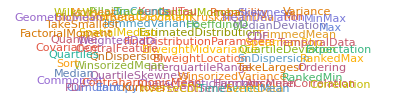

### Hypothesis Testing

Hypothesis tests give quantitative answers to common questions, such as how good the fit is between data and a particular distribution, whether these distributions have the same mean or median, and whether these datasets have the same variability. The Wolfram Language provides high-level functions for these types of questions and will automatically select the tests applicable for the data and distributions given.

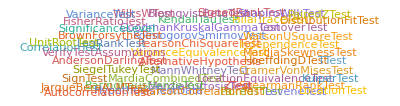

## Introduction to Distributions

The collection of parametric distributions in the Wolfram Language has been selected in order to provide complete modeling frameworks for a variety of areas.  The result is the most extensive collection of parametric distributions ever assembled, including various univariate and multivariate continuous and discrete distributions.  Similarly the Wolfram Language has Nonparametric Distributions, that can be directly constructed from data, Derived Distributions (distributions that can be constructed from other distributions) and Formula Distributions

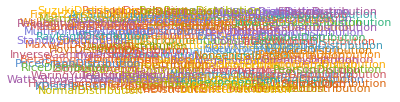

Once you have defined your distribution, you can extract different properties from it. Let’s try and evaluate a few of them

### Probability and Expectation

Discrete univariate probabilities

```mathematica
Probability[x≥1,x\[Distributed]BinomialDistribution[n,p]]
```

Nonlinear conditions

```mathematica
Probability[(x-3)^2≥x,x\[Distributed]ZipfDistribution[ρ]]
```

Logical combinations

```mathematica
Probability[k^2>10||k<2,k\[Distributed]PoissonDistribution[λ]]
```

Multivariate probabilities

```mathematica
Probability[X≤1/2&&Y≤1,{X,Y}\[Distributed]DirichletDistribution[{1,2,3}]]
```

Conditional probabilities

```mathematica
Probability[x^2>1\[Conditioned]x>1/2,x\[Distributed]LaplaceDistribution[0,1/2]]
```

Polynomial expectation

```mathematica
Expectation[2x^4+3,x\[Distributed]NormalDistribution[]]
```

Expectation of an arbitrary expression

```mathematica
Expectation[E^(-x)+3x,x\[Distributed]ChiSquareDistribution[ν]]
```

## Distribution Properties

### Distribution Functions

In this section, you will see how to obtain the probability density function PDF (or probability mass function in discrete cases), cumulative density function CDF, survival function SurvivalFunctionand HazardFunction and visualize them using different built-in visualization techniques. For the different classes of distributions (depending on discrete versus continuous or univariate versus multivariate), the visualization function used will vary. First, look at the definitions of these functions:

1234

Univariate continuous:

```mathematica
Manipulate[Plot[Table[func[NormalDistribution[0,σ],x],{σ,{.75,1,2}}]//Evaluate,{x,-6,6},Filling->Axis],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

Univariate discrete:

```mathematica
Manipulate[DiscretePlot[Table[func[GeometricDistribution[p],k],{p,{0.1,0.2,0.5}}]//Evaluate,{k,0,14},ExtentSize->Right],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

Multivariate continuous:

```mathematica
Manipulate[Plot3D[func[BinormalDistribution[1/2],{x,y}],{x,-1,3},{y,-1,3},PlotRange->All,MaxRecursion->0],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

Multivariate discrete:

```mathematica
Manipulate[DiscretePlot3D[func[MultinomialDistribution[10,{1/3,2/3}],{x,y}],{x,-1,7},{y,-1,7},ExtentSize->Right],{{func,PDF,"ProbabilityFunction"},{PDF,CDF,SurvivalFunction,HazardFunction}}]
```

### Moments

In the Wolfram Language, you can obtain the raw moment, Moment; the moment about the mean, CentralMoment; the factorial moment, FactorialMoment; and the cumulant, Cumulant. The formulas used in these computations follow:

123

Compute the second Moment μ_2 of a univariate distribution:

```mathematica
Moment[NormalDistribution[μ,σ],2]
```

The second and third instances of CentralMoment as measures of dispersion and skewness:

```mathematica
CentralMoment[NormalDistribution[μ,σ],2]
```

Zero-skewed, positively skewed and negatively skewed distributions:

```mathematica
{CentralMoment[NormalDistribution[1,2],3], CentralMoment[ChiSquareDistribution[2],3],CentralMoment[GumbelDistribution[1,2],3]}//N
```

Tabulate moments up to order 5 for the GammaDistribution:

```mathematica
MomentTabView[GammaDistribution[α,β],5]
```

1234

## Simulation of Distributions

Univariate Continuous

```mathematica
data=RandomVariate[NormalDistribution[1,3],10^4];
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-9,9},PlotStyle->Thick]]
```

Multivariate Discrete

```mathematica
data=RandomVariate[MultivariatePoissonDistribution[1,{2,3}],10^4];
{Histogram3D[data,20,"Probability",PlotRange->{{0,10},{0,10},All}],
DiscretePlot3D[PDF[MultivariatePoissonDistribution[1,{2,3}],{x,y}],{x,0,10},{y,0,10},PlotRange->All,ExtentSize->Full]}
```

Mixture Distributions

```mathematica
𝒟 =MixtureDistribution[{1,3}, {NormalDistribution[0,1],NormalDistribution[6,2]}];
data = RandomVariate[𝒟,10^5];
Show[Histogram[data,50,"PDF"],Plot[PDF[𝒟,x],{x,-20,20}]]
```

## Fitting Data to Known Distributions

The lottery.txt file contains information on the Maryland Pick 3 lottery. The winning numbers are returned as three-digit numbers from 000 to 999. If the lottery is fair, you would expect the winning numbers to come from a uniform distribution defined on the interval {0,999}. Let’s go ahead and check that visually and quantitatively.

### Visualizations

Import the data:

```mathematica
lotDat=Import[FileNameJoin[{NotebookDirectory[],"lottery.txt"}],"List"];
```

Visualize the data by plotting a Histogram, along with DistributionChart and BoxWhiskerChart. Finally, QuantilePlot will help compare the data to a UniformDistribution.

```mathematica
GraphicsRow[{Histogram[lotDat,10,PlotLabel-> "Histogram"],
DistributionChart[lotDat,PlotLabel-> "DistributionChart"],
BoxWhiskerChart[lotDat,PlotLabel-> "BoxWhiskerChart"],
QuantilePlot[lotDat,UniformDistribution[{0,999}],PlotLabel-> "QuantilePlot"]},ImageSize->1000]
```

### Quantitative fitting

Now let’s do a quantitative test. DistributionFitTest can be used to determine if your assumptions about the fairness of the lottery are reasonable.

```mathematica
ftTst= DistributionFitTest[lotDat,UniformDistribution[{0,999}],"HypothesisTestData"]
```

Here are the properties available from the test.

```mathematica
ftTst["Properties"]
```

The tests that are relevant for this particular case:

```mathematica
ftTst["TestDataTable",All]
```

```mathematica
Column[{Style[ftTst["ShortTestConclusion"],"Text"],Style[ftTst["TestConclusion"],"Text"]},Frame->True]
```

## Fitting Data to Distributions

In the case that you have no prior knowledge of the distribution to fit the data points, there are two alternatives:
 	i)  Use a nonparametric distribution estimator.
 	ii) Use FindDistribution to select parametric distribution based on parameter fit.

In the US, the largest wind power center is situated at Alta Wind Energy Center in California. Visualize the location and then analyze the wind data obtained there, using the built-in functions in the Wolfram Language:

```mathematica
GeoGraphics[GeoMarker[Entity["Company","AltaWindEnergyCenter::4h269"]],GeoRange->Quantity[200, "Kilometers"]]
```

-Graphics-

In this example, you will try to fit wind speed data to a parametric as well as a nonparametric distribution and find the probability that the wind speed is greater than the cutoff wind speed required to generate power.

### Getting the Data via WeatherData

In this example, information from WeatherData is used to investigate the feasibility of using wind to generate electricity. First obtain the data, then clean it to remove the missing values:

```mathematica
(*wndData=TimeSeries[WeatherData[GeoPosition[Entity["Company","AltaWindEnergyCenter::4h269"]], "MeanWindSpeed",{{2000,1,1},Date[],"Day"}],MissingDataMethod->Automatic];*)
dataclean=QuantityMagnitude@wndData["Values"];
```

```mathematica
DateListPlot[wndData]
```

Visualize the data in histograms for the PDF and CDF:

```mathematica
GraphicsRow[{histplotpdf,histplotcdf}={Histogram[QuantityMagnitude@wndData,45,"PDF",PlotLabel->"PDF"],Histogram[QuantityMagnitude@wndData,45,"CDF",PlotLabel->"CDF"]},ImageSize-> Large]
```

### Fitting to a Nonparametric Distribution

Since wind speed can be assumed to vary continuously, estimate a distribution for observations using the SmoothKernelDistribution function. Find an estimated distribution and visualize the results. This assumes the data comes from a continuous distribution:

```mathematica
Subscript[𝒟, e]=SmoothKernelDistribution[dataclean]
```

Visualize how good the fit is and conclude with a quantitative estimate:

```mathematica
GraphicsRow[{Show[{
histplotpdf,
estplot= Plot[PDF[Subscript[𝒟, e],x],{x,0,90},PlotStyle->Thick]
}],Show[{
histplotcdf,
estplot= Plot[CDF[Subscript[𝒟, e],x],{x,0,90},PlotStyle->Thick]}
]},ImageSize-> Large]
```

```mathematica
tstData=DistributionFitTest[dataclean,Subscript[𝒟, e],"HypothesisTestData"];
tstData["TestDataTable", All]
```

```mathematica
Column[{Style[tstData["ShortTestConclusion"],"Text"],Style[tstData["TestConclusion"],"Text"]},Frame->True]
```

### Fitting to Parametric Distributions

An alternate approach would be to fit the data to known parametric distributions using FindDistribution:

```mathematica
Subscript[𝒟, p]=FindDistribution[dataclean]
```

```mathematica
tstData=DistributionFitTest[dataclean,Subscript[𝒟, p],"HypothesisTestData"];
tstData["TestDataTable", All]
```

Visualize how good the fit is:

```mathematica
GraphicsRow[{Show[{
histplotpdf,
estplot= Plot[PDF[Subscript[𝒟, p],x],{x,0,90},PlotStyle->Thick]
}],Show[{
histplotcdf,
estplot= Plot[CDF[Subscript[𝒟, p],x],{x,0,90},PlotStyle->Thick]}
]},ImageSize-> Large]
```

The cutoff wind speed for wind generation is approximately 12 km/h. You can find out what probability each of these models predicts for successful wind power generation:

```mathematica
Probability[x>12.0,x\[Distributed] Subscript[𝒟, p]]
```

```mathematica
Probability[x>12.0,x\[Distributed] Subscript[𝒟, e]]
```

## Linear Models

LinearModelFit produces a linear model of the form ŷ=β_0+β_1 f_1+β_2 f_2+… under the assumption that the original y_i are independent normally distributed with mean (ŷ)_i and common standard deviation.

In this example we are going to fetch the population and GDP of India from the Wolfram Data resources and then do analysis on the GDP per capita for the more recent years.

### Data manipulation

Let us obtain the population of India for the last 5 decades The population data returns as a TimeSeries object and the use of Normal returns the data in the form of a list.

```mathematica
(*popdat=Normal@EntityValue[Entity["Country","India"],EntityProperty["Country","Population",{"Date"-> Interval[{DateObject[{1967},"Year","Gregorian",-5.],DateObject[{2017},"Year","Gregorian",-5.]}]}]]*)
```

Since the time series data has a quantity, we just convert it to the numbers using QuantityMagnitude and convert the date objects to the corresponding year so that it can be fed into the LinearModelFit.

```mathematica
Pop=Table[{1966+i,QuantityMagnitude@popdat[[i,2]]},{i,1,Length[popdat]}]
```

Let us visualize the growth in the population, which seems to be very linear.

```mathematica
ListPlot[Pop, Joined-> False, PlotStyle->Red]
```

### Fitting a linear model

Let us fit the data to a linear model, and then visualize the fit to see if there is any variability unaccounted for:

```mathematica
popfit= LinearModelFit[Pop,t,t]
```

```mathematica
Show[ListPlot[Pop,Joined->False,PlotStyle->Red],Plot[popfit[t],{t,1967,2017}]]
```

Obtain the available properties related to the LinearModelFit and evaluate a few of them.

```mathematica
Framed[NiceTable[Style[#,14,"Text"]&/@popfit["Properties"]],RoundingRadius-> 12,FrameMargins-> 15]
```

```mathematica
{popfit["ANOVATable"],popfit["AdjustedRSquared"],popfit["AICc"]}
```

### Fitting several models

Fit multiple models simultaneously with different polynomial degrees in time:

```mathematica
multiFit= Table[LinearModelFit[Pop,basis,t],{basis,{t,t^Range[0,2],t^Range[0,4],t^Range[0,5],t^Range[0,6],t^Range[0,7]}}]
```

Obtain the relevant statistics for the fitted model and compare the fitted models:

```mathematica
Through[multiFit["AdjustedRSquared"]]
```

```mathematica
Through[multiFit["AIC"]]
```

### GDP per capita fit

Analyzing the GDP Per Capita for India since 2000’s post the 1990’s economic depression.

```mathematica
(*GDP=Normal@EntityValue[Entity["Country","India"],EntityProperty["Country","GDP",{"Date"-> Interval[{DateObject[{2000},"Year","Gregorian",-5.],DateObject[{2015},"Year","Gregorian",-5.]}]}]]*)
(*Pop2000=Normal@EntityValue[Entity["Country","India"],EntityProperty["Country","Population",{"Date"-> Interval[{DateObject[{2000},"Year","Gregorian",-5.],DateObject[{2015},"Year","Gregorian",-5.]}]}]]*)
```

```mathematica
GDPperCapita=Table[{i+1999,QuantityMagnitude@GDP[[i,2]]/QuantityMagnitude@Pop2000[[i,2]]},{i,1,Length[GDP]}]
```

```mathematica
GDPperCapitafit= LinearModelFit[GDPperCapita,t^Range[0,3],t]
```

Plot the fit to the actual data:

```mathematica
Show[ListPlot[GDPperCapita,PlotStyle->Red], Plot[GDPperCapitafit[t], {t, 2000, 2015}, PlotRange->All, PlotStyle->Black]]
```

Plot the Residuals and Cook’s Distance of the best fit:

```mathematica
GraphicsRow[{ListPlot[GDPperCapitafit["FitResiduals"],Filling->Axis,Frame->True,PlotRange->All,PlotLabel->"Residuals",PlotStyle->Black],ListPlot[GDPperCapitafit["CookDistances"],PlotStyle->Black,Filling->Axis,Frame->True,PlotRange->All,PlotLabel->"Cook's Distances"]},ImageSize->700]
```

## Nonlinear Model Fit

Linear models are fitted using linear algebra, a process that is, in most cases, robust and fast. Nonlinear models, on the other hand, require the construction of a merit function and then minimizing the merit function based on varying a set of parameters present in the model. This process can be slow and often requires more attention on the part of the statistician.

In this example, we will import a file that contains data on total production from different sources of energy for the year 2010. We will look at the renewable energy sources and try to find a relationship that defines the growth in the production of renewable sources over the time. For convenience the data cleaning is done in the initialization cells, which is present at the end of the notebook.

### Fitting a nonlinear model

First let us visualize the data we imported:

```mathematica
ListPlot[elecdata,Mesh-> All]
```

```mathematica
Clear[a,b,c,t];
model=NonlinearModelFit[elecdata,a+ⅇ^(b (t-c)),{a,b,{c,1990}},t]
```

```mathematica
model["BestFit"]
```

The fit appears to be a good one.

```mathematica
Show[
Plot[model[t],{t,1993.5,2008.5},PlotStyle->{Pink,Thick},PlotRange->All],
ListLinePlot[elecdata,Mesh-> All,PlotMarkers-> Automatic]
]
```

Because you are using a nonlinear model here, the property list is shorter than with LinearModelFit.

```mathematica
NiceTable[Style[#,12,"Text"]&/@model["Properties"]]
```

```mathematica
model[{"ANOVATable","FitCurvatureTable","ParameterBias","AICc"}]
```

## Generalized Linear Models

Generalized linear models are a family of regression models, with the form ŷ==g^-1(β_0+β_1 x_1+β_2 x_2+…) and the Wolfram Language has a built-in framework, GeneralizedLinearModelFit, for working with such problems. Other than the two components we briefly discussed before for simple regression problems, the independent terms (x_1,x_2...), and the response variable (ŷ), we have the link function (g) which specifies how the expected values of the response related to a linear change in the independent variables. 

Depending on the LinkFunction, different models of regression can be created:

"Link" | "Regression Type"
Identity | Simple Linear Regression
Logit | Logistic Regression
Log | Poisson Regression
Reciprocal | Gamma Regression
Inverse Square | InverseGaussian Regression

Let us consider an example using one of these type of Regression, say the Poisson Regression:

### Poisson Regression

A dataset from Australia will be used that gives the number of deaths from AIDS on a quarterly basis, covering the time period from January 1983 to June 1986.

```mathematica
aidsDat={0, 1, 2, 3, 1, 4, 9, 18, 23, 31, 20, 25, 37, 45};
```

The independent variables are just uniformly spaced time values, so take them to be 1-Length[aidsDat]. Fit two models, the first where just the count is taken and the second where the logarithm of the count is used. Use ExponentialFamily → “Poisson” because the responses are counts.

```mathematica
mod1=GeneralizedLinearModelFit[aidsDat,{1,x},x,ExponentialFamily->"Poisson"];
```

```mathematica
mod2=GeneralizedLinearModelFit[aidsDat,{1,Log[x]},x,ExponentialFamily->"Poisson"]
```

Taking a look at the parameter tables shows that the estimates are more "significant" for the second model, even though the model is no more complex.

```mathematica
Row[{mod1["ParameterTable"],"   ",mod2["ParameterTable"]}]
```

Taking a look at the plot and giving AIC shows that the log-based model also fits much better. Both of these models are better in terms of reflecting the true nature of the data than a linear model and fit better (according to AIC). If the dataset was larger, it would likely be possible to show that the linear model has residuals with bad properties (but the dataset is just too small to do that).

```mathematica
mod3 = LinearModelFit[aidsDat, {1, x}, x];
```

```mathematica
Show[Plot[{mod3[t],mod1[t],mod2[t]},{t,1,14},PlotLegends->{Row[{"Linear AIC: ",mod3["AIC"]}],Row[{"GLM {1,x} AIC: ",mod1["AIC"]}],Row[{"GLM {1,Log[x]} AIC: ",mod2["AIC"]}]}],ListPlot[aidsDat,PlotMarkers-> Automatic]]
```

## Generalized Linear Models: Logistic Models

This dataset indicates the presence/absence of gold deposit as a function of water/chemical factors: As, Sb, and presence/absence of lineament in the Hutti-Maski Schist Belt, Raichur, Karnataka, India. 
The presence/absence of gold deposit is fitted in a logistic regression model to the Arsenic and Antimony level, and the lineament proximity to water.

### Data import and cleaning

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"gold_target1.dat"}]];
```

The last five rows are blank and the data is in string format. Let us convert it to numbers and get rid of the last five rows:

```mathematica
golddat=ToExpression@data[[;;-5]];
```

### Fitting a logistic model

```mathematica
(mod1=GeneralizedLinearModelFit[golddat,{As,Sb,Ln},{As,Sb,Ln},ExponentialFamily->"Binomial"])//Normal
```

A logistic model is commonly used. LogitModelFit can be obtained from GeneralizedLinearModelFit by setting ExponentialFamily to Binomial.

```mathematica
mod2=(LogitModelFit[golddat,{As,Sb,Ln},{As,Sb,Ln}])//Normal
```

Computing the statistics and visualizing the residuals:

```mathematica
{mod1["ParameterTable"],ListPlot[mod1["FitResiduals"],PlotStyle->Red, Filling-> Axis,PlotRange-> All,PlotLegends->Row[{"BIC: ",mod1["BIC"],"   AIC: ",mod1["AIC"]}],ImageSize->400]}
```

Source: N.R. Sahoo and H.S. Pandalai (1999). “Integration of Sparse GeologiInformation in Gold Targeting Using Logistic Regression Analysis in the  Hutti-Maski Schist Belt, Raichur, Karnataka, India - A Case Study,” Natural Resources Research, Vol. 8, #3, pp. 233-250.

## Generalized Linear Models : Link Function

The canonical link functions and their corresponding type of regression has been discussed. Now let’s focus on other link functions that can be used for Binomial data: 

"Link" | "Formula"
Probit | √2 InverseErf[-1+2 y]
Cauchit | tan(π (x-1/2))
LogLog | -log(-log(y))
LogComplement | log(1-y)
ComplementaryLogLog | Log[-Log[1-y]]
OddsPowerLink | Piecewise[{{((y/(1-y))^α-1)/α, α≠0}, {log(y/(1-y)), α==0}}]
NegativeBinomialLink | log((α y)/(α y+1))

Let us consider an example using one of these link function, the NegativeBinomialLink.

### Import and clean data

In this example we will try to fit the terrorism (incidence and casualties) in different provinces of Afghanistan to various variables. The variables include: opium production, population, area, mountainous, nutrition, literacy, drinking water, roads, infant mortality, Pashtun majority, and foreign troops. This data is aggregated over years (n=33). Finally we want to conclude what are the most important factors.

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"afghan_terror.dat"}]];
```

Let us look at how the data is interpreted in Wolfram Language:

```mathematica
data[[1]]//InputForm
```

### Fitting the number of incidents with the NegativeBinomialLink

First we will try to fit the number of incidents of terrorism occurring. Since the first entry is not one of the variables, we can eliminate it, and then modify the data so that we can fit the number of incidents with the other variable:

```mathematica
dataincidents=data[[All,2;;]]/.{inc_,death_,opium_,pop_,area_,mountain_,literacy_,water_,food_,road_,infmortality_,Pashtun_,foreign_}-> {opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign,inc};
```

```mathematica
(mod1=GeneralizedLinearModelFit[dataincidents,{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},ExponentialFamily->"Poisson",LinkFunction-> "NegativeBinomialLink"])
```

```mathematica
ListPlot[mod1["FitResiduals"],PlotStyle->Red, Filling-> Axis,PlotRange-> All,PlotLegends->Row[{"BIC: ",mod1["BIC"],"   AIC: ",mod1["AIC"]}]]
```

### Fitting the number of deaths

In this section we will analyse the number of deaths. For that let us modify our data accordingly.

```mathematica
datadeaths=data[[All,2;;]]/.{inc_,death_,opium_,pop_,area_,mountain_,literacy_,water_,food_,road_,infmortality_,Pashtun_,foreign_}-> {opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign,death};
```

Next let us try to fit the data using all the variables:

```mathematica
(mod1=GeneralizedLinearModelFit[datadeaths,{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},ExponentialFamily->"Gaussian"])//Normal
```

```mathematica
{mod1["ParameterTable"],ListPlot[mod1["FitResiduals"],PlotStyle->Red, Filling-> Axis,PlotRange-> All,PlotLegends->Row[{"AICc: ",mod1["BIC"],"   AIC: ",mod1["AIC"]}],ImageSize->500]}
```

However, is this the best model? To find out the best model fit, let us consider all subsets of the variables and find out the fit which corresponds to the highest of a statistical inference parameter, here the AICc is chosen.

```mathematica
sub=Table[Join[{i},GeneralizedLinearModelFit[datadeaths,i,{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},ExponentialFamily->"Gaussian"][{"AIC","BIC","LikelihoodRatioIndex","PearsonChiSquare"}]],{i,Subsets[{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign}]}];
```

Thus we see that the most important variables are opium production, area, mountain, water, and road, and infant mortality.

```mathematica
Grid[Join[{{"Model","AICc","BIC","LikelihoodRatioIndex","PearsonChiSquare"}},Take[SortBy[sub,#[[2]]&],5]],Alignment->Left]
```

Source: J.A. Piazza (2012). “The Opium Trade and Patterns of Terrorism in the Provinces of Afghanistan: An Empirical Analysis,” Terrorism and Political Violence, Vol. 24, pp. 213-234

## Time Series Models: Airline Passenger Data

Time series refers to a sequence of observations following each other in time, where adjacent observations are correlated. This can be used to model, simulate, and forecast behavior for a system. Time series models are frequently used in fields such as economics, finance, biology, and engineering. The Wolfram Language provides a full suite of time series functionality, including standard models such as MA, AR, and ARMA, as well as several extensions. Time series models can be simulated, estimated from data, and used to produce forecasts of future behavior.

The existing time series models in the Wolfram Language:

Model Type | Models
Basic Auto-Regressive and Moving Average Processes   | MAProces| ARProcess | ARMAProcess
Integrated and Seasonal Processes | ARIMAProcess | SARIMAProcess  | SARMA Process | FARIMA Process
Generalized Auto-regressive Conditional Heteroskedasicity Processes | ARCHProcess |GARCHProcess

The following data contains the monthly total number of US international airline passengers (in thousands) from January 1949 to December 1960. This a standard “text book” data set because it contains seasonality integrated with autoregressive and Moving Average processes.

```mathematica
passengers=TimeSeries[…];
```

Split the data at January 1958:

```mathematica
before1958=TimeSeriesWindow[passengers,{Automatic,"December 1957"}];
since1958=TimeSeriesWindow[passengers,{"January 1958",Automatic}];
```

```mathematica
plot=DateListPlot[{before1958,since1958},Joined->True,PlotLegends->{"Before 1958","After 1958"}]
```

Fit the Model using TimeSeriesModelFit:

```mathematica
tsm=TimeSeriesModelFit[before1958]
```

Visualize the Model Fit and the Forecast:

```mathematica
DateListPlot[{before1958,since1958,Table[{t,tsm[t]},{t,DateRange["January 1958","December 1960","Month"]}]},Joined->True,PlotLegends->{"Before 1958","After 1958","Forecast"}]
```

## Time Series Models: Weather Data at Your Present Location

Let us gather the temperature in your present location for the last 10 years and plot the data.

```mathematica
today=DateValue[Today,{"Year","Month"}];
start=DateValue[DatePlus[Today,{-10,"Year"}],{"Year","Month"}];
tspec = {start,today,"Month"};
temp=TimeSeries[WeatherData[FindGeoLocation[],"Temperature",tspec,"NonMetricValue"],{start,Automatic,"Month"}]
```

Clearly there is a seasonal variation in the temperatures

```mathematica
DateListPlot[temp,{Automatic,today},Joined->True,FrameLabel->Automatic]
```

Let us automatically fit the data to a time series model.

```mathematica
tsm=TimeSeriesModelFit[temp]
```

Next let us forecast the temperature for the next year, along with the PredictionLimits. Prediction limits are slightly higher than the confidence intervals.

```mathematica
fdates=DateRange[today,DatePlus[today,{1,"Year"}],"Month"];
```

```mathematica
forecast=tsm/@fdates;
bands=tsm["PredictionLimits"][#]&/@fdates;
```

```mathematica
DateListPlot[{bands⟦All,1⟧,forecast,bands⟦All,2⟧},{today, Automatic,"Month"},Filling->{1->{3}},Joined->True,PlotStyle->{Gray,Automatic}]
```

## Glossary

AdjustedRSquared | AIC | AICc | ANOVATable | Axis
BestFit | BIC | Binomial | BinomialDistribution | BinormalDistribution
BoxWhiskerChart | Cases | CDF | ChiSquareDistribution | Column
Cook's Distances | Date | DatePlus | DateRange | DateValue
DirichletDistribution | DiscretePlot | DiscretePlot3D | DistributionChart | DistributionFitTest
Evaluate | ExponentialFamily | ExtentSize | FileNameJoin | Filling
FindDistribution | FindGeoLocation | FitCurvatureTable | FitResiduals | Frame
Framed | FrameMargins | GammaDistribution | Gaussian | GeneralizedLinearModelFit
GeoGraphics | GeoMarker | GeometricDistribution | GeoRange | GraphicsRow
Grid | HazardFunction | Histogram | ImageSize | Import
Join | LaplaceDistribution | Large | Length | LikelihoodRatioIndex
LinearModelFit | LinkFunction | ListLinePlot | ListPlot | LogitModelFit
Manipulate | MaxRecursion | MixtureDistribution | MultivariatePoissonDistribution | NegativeBinomialLink
NonlinearModelFit | Normal | NormalDistribution | NotebookDirectory | NumericQ
ParameterBias | ParameterTable | PDF | PearsonChiSquare | Plot
Plot3D | PlotLabel | PlotMarkers | PlotRange | PlotStyle
Poisson | PoissonDistribution | PredictionLimits | Probability | QuantilePlot
QuantityMagnitude | RandomVariate | Residuals | RoundingRadius | Show
SmoothKernelDistribution | SortBy | Style | Subsets | SurvivalFunction
Table | Take | Thick | TimeSeries | TimeSeriesModelFit
TimeSeriesWindow | Today | UniformDistribution | WeatherData | ZipfDistribution

## Initialize Slide

### Display functions

```mathematica
CellDisplay[expr_]:=CellPrint[ExpressionCell[expr,"Output",Background->None,ShowCellLabel->False,CellFrame->False,CellMargins->{{100,100},{40,0}},"Output",GeneratedCell->False]];
MomentGrid[list_,type_]:=
Grid[Transpose@{list},Alignment->{Left,Automatic},Background->{None,{{Lighter[Blend[Switch[type,Moment,{Blue,Green},CentralMoment,{Red,Orange},FactorialMoment,{Magenta,Cyan},Cumulant,{Purple,Red}]],.8],White}}},Dividers->{None,{Darker[Gray,.6],{False},Darker[Gray,.6]}},ItemSize->30];
MomentTabView[dist_,n_Integer?Positive]:=
CellDisplay@TabView[{"Moment"->MomentGrid[Table[Moment[dist,k],{k,n}],Moment],"CentralMoment"->MomentGrid[Table[CentralMoment[dist,k],{k,n}],CentralMoment],"FactorialMoment"->MomentGrid[Table[FactorialMoment[dist,k],{k,n}],FactorialMoment],"Cumulant"->MomentGrid[Table[Cumulant[dist,k],{k,n}],Cumulant]}];
```

### wndData

```mathematica
(*wndData=TimeSeries[WeatherData[GeoPosition[Entity["Company","AltaWindEnergyCenter::4h269"]], "MeanWindSpeed",{{2000,1,1},Date[],"Day"}],MissingDataMethod->Automatic];*)
```

```mathematica
wndData=TimeSeries[…];
```

### fshDat

```mathematica
fshDat={{5.9,7.5,8.4,8.8,24.,16.},{32.,12.5,13.7,14.7,24.,13.6},{40.,13.8,15.,16.,23.9,15.2},{51.5,15.,16.2,17.2,26.7,15.3},{70.,15.7,17.4,18.5,24.8,15.9},{100.,16.2,18.,19.2,27.2,17.3},{78.,16.8,18.7,19.4,26.8,16.1},{80.,17.2,19.,20.2,27.9,15.1},{85.,17.8,19.6,20.8,24.7,14.6},{85.,18.2,20.,21.,24.2,13.2},{110.,19.,21.,22.5,25.3,15.8},{115.,19.,21.,22.5,26.3,14.7},{125.,19.,21.,22.5,25.3,16.3},{130.,19.3,21.3,22.8,28.,15.5},{120.,20.,22.,23.5,26.,14.5},{120.,20.,22.,23.5,24.,15.},{130.,20.,22.,23.5,26.,15.},{135.,20.,22.,23.5,25.,15.},{110.,20.,22.,23.5,23.5,17.},{130.,20.5,22.5,24.,24.4,15.1},{150.,20.5,22.5,24.,28.3,15.1},{145.,20.7,22.7,24.2,24.6,15.},{150.,21.,23.,24.5,21.3,14.8},{170.,21.5,23.5,25.,25.1,14.9},{225.,22.,24.,25.5,28.6,14.6},{145.,22.,24.,25.5,25.,15.},{188.,22.6,24.6,26.2,25.7,15.9},{180.,23.,25.,26.5,24.3,13.9},{197.,23.5,25.6,27.,24.3,15.7},{218.,25.,26.5,28.,25.6,14.8},{300.,25.2,27.3,28.7,29.,17.9},{260.,25.4,27.5,28.9,24.8,15.},{265.,25.4,27.5,28.9,24.4,15.},{250.,25.4,27.5,28.9,25.2,15.8},{250.,25.9,28.,29.4,26.6,14.3},{300.,26.9,28.7,30.1,25.2,15.4},{320.,27.8,30.,31.6,24.1,15.1},{514.,30.5,32.8,34.,29.5,17.7},{556.,32.,34.5,36.5,28.1,17.5},{840.,32.5,35.,37.3,30.8,20.9},{685.,34.,36.5,39.,27.9,17.6},{700.,34.,36.,38.3,27.7,17.6},{700.,34.5,37.,39.4,27.5,15.9},{690.,34.6,37.,39.3,26.9,16.2},{900.,36.5,39.,41.4,26.9,18.1},{650.,36.5,39.,41.4,26.9,14.5},{820.,36.6,39.,41.3,30.1,17.8},{850.,36.9,40.,42.3,28.2,16.8},{900.,37.,40.,42.5,27.6,17.},{1015.,37.,40.,42.4,29.2,17.6},{820.,37.1,40.,42.5,26.2,15.6},{1100.,39.,42.,44.6,28.7,15.4},{1000.,39.8,43.,45.2,26.4,16.1},{1100.,40.1,43.,45.5,27.5,16.3},{1000.,40.2,43.5,46.,27.4,17.7},{1000.,41.1,44.,46.6,26.8,16.3}};
```

### Excel file clean up

Initialization code/ Data cleaning for Slide You will look at renewables up through the year 2010. First, determine the number of the column containing the data you want to use. Referring to your table above, you see you want rows 4 through 57 and columns 1 and 9. Using pattern matching, convert the strings to numbers and extract only the yearly totals.Using replacement rules, “clean up” the rows corresponding to the years 2006, 2007, and 2008.

```mathematica
electricData= Import[FileNameJoin[{NotebookDirectory[],"epmxlfile1_1.xls"}],{"Data",1}];
Dimensions[electricData];
Position[electricData,"Other Renewables[4]"];
renewables=electricData[[4;;57,{1,9}]];
yearTots=Cases[renewables,{_?NumericQ|"Total",_?NumericQ}];
elecdata=ReplacePart[yearTots,{{-3,1}-> 2006.,{-2,1}->2007.,{-1,1}->2008.}];
```

### United States data

```mathematica
(*popdat=Normal@EntityValue[Entity["Country","UnitedStates"],EntityProperty["Country","Population",{"Date"-> Interval[{DateObject[{1967},"Year","Gregorian",-5.],DateObject[{2017},"Year","Gregorian",-5.]}]}]];*)
popdat={{DateObject[{1967,1,1},"Day","Gregorian",-5.],Quantity[1.98712*^8, "People"]},{DateObject[{1968,1,1},"Day","Gregorian",-5.],Quantity[2.00706*^8, "People"]},{DateObject[{1969,1,1},"Day","Gregorian",-5.],Quantity[2.02677*^8, "People"]},{DateObject[{1970,1,1},"Day","Gregorian",-5.],Quantity[209463865, "People"]},{DateObject[{1971,1,1},"Day","Gregorian",-5.],Quantity[211355529, "People"]},{DateObject[{1972,1,1},"Day","Gregorian",-5.],Quantity[213250350, "People"]},{DateObject[{1973,1,1},"Day","Gregorian",-5.],Quantity[215164616, "People"]},{DateObject[{1974,1,1},"Day","Gregorian",-5.],Quantity[217113584, "People"]},{DateObject[{1975,1,1},"Day","Gregorian",-5.],Quantity[219108358, "People"]},{DateObject[{1976,1,1},"Day","Gregorian",-5.],Quantity[221161377, "People"]},{DateObject[{1977,1,1},"Day","Gregorian",-5.],Quantity[223274855, "People"]},{DateObject[{1978,1,1},"Day","Gregorian",-5.],Quantity[225436004, "People"]},{DateObject[{1979,1,1},"Day","Gregorian",-5.],Quantity[227624232, "People"]},{DateObject[{1980,1,1},"Day","Gregorian",-5.],Quantity[229825004, "People"]},{DateObject[{1981,1,1},"Day","Gregorian",-5.],Quantity[232035086, "People"]},{DateObject[{1982,1,1},"Day","Gregorian",-5.],Quantity[234261242, "People"]},{DateObject[{1983,1,1},"Day","Gregorian",-5.],Quantity[236510688, "People"]},{DateObject[{1984,1,1},"Day","Gregorian",-5.],Quantity[238794274, "People"]},{DateObject[{1985,1,1},"Day","Gregorian",-5.],Quantity[241119752, "People"]},{DateObject[{1986,1,1},"Day","Gregorian",-5.],Quantity[243495805, "People"]},{DateObject[{1987,1,1},"Day","Gregorian",-5.],Quantity[245920994, "People"]},{DateObject[{1988,1,1},"Day","Gregorian",-5.],Quantity[248381577, "People"]},{DateObject[{1989,1,1},"Day","Gregorian",-5.],Quantity[250857751, "People"]},{DateObject[{1990,1,1},"Day","Gregorian",-5.],Quantity[253339097, "People"]},{DateObject[{1991,1,1},"Day","Gregorian",-5.],Quantity[255807342, "People"]},{DateObject[{1992,1,1},"Day","Gregorian",-5.],Quantity[258275919, "People"]},{DateObject[{1993,1,1},"Day","Gregorian",-5.],Quantity[260803255, "People"]},{DateObject[{1994,1,1},"Day","Gregorian",-5.],Quantity[263468979, "People"]},{DateObject[{1995,1,1},"Day","Gregorian",-5.],Quantity[266323717, "People"]},{DateObject[{1996,1,1},"Day","Gregorian",-5.],Quantity[269393632, "People"]},{DateObject[{1997,1,1},"Day","Gregorian",-5.],Quantity[272643340, "People"]},{DateObject[{1998,1,1},"Day","Gregorian",-5.],Quantity[275986072, "People"]},{DateObject[{1999,1,1},"Day","Gregorian",-5.],Quantity[279300030, "People"]},{DateObject[{2000,1,1},"Day","Gregorian",-5.],Quantity[282496310, "People"]},{DateObject[{2001,1,1},"Day","Gregorian",-5.],Quantity[285544778, "People"]},{DateObject[{2002,1,1},"Day","Gregorian",-5.],Quantity[288467308, "People"]},{DateObject[{2003,1,1},"Day","Gregorian",-5.],Quantity[291290823, "People"]},{DateObject[{2004,1,1},"Day","Gregorian",-5.],Quantity[294063120, "People"]},{DateObject[{2005,1,1},"Day","Gregorian",-5.],Quantity[296820296, "People"]},{DateObject[{2006,1,1},"Day","Gregorian",-5.],Quantity[299564470, "People"]},{DateObject[{2007,1,1},"Day","Gregorian",-5.],Quantity[302284564, "People"]},{DateObject[{2008,1,1},"Day","Gregorian",-5.],Quantity[304989064, "People"]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity[307686729, "People"]},{DateObject[{2010,1,1},"Day","Gregorian",-5.],Quantity[310383948, "People"]},{DateObject[{2011,1,1},"Day","Gregorian",-5.],Quantity[313232044, "People"]},{DateObject[{2012,1,1},"Day","Gregorian",-5.],Quantity[316265537, "People"]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity[319330342, "People"]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity[322422965, "People"]},{DateObject[{2015,1,1},"Day","Gregorian",-5.],Quantity[325539790, "People"]},{DateObject[{2016,1,1},"Day","Gregorian",-5.],Quantity[328677531, "People"]},{DateObject[{2017,1,1},"Day","Gregorian",-5.],Quantity[331833494, "People"]}};
(*GDP=Normal@EntityValue[Entity["Country","UnitedStates"],EntityProperty["Country","GDP",{"Date"-> Interval[{DateObject[{2000},"Year","Gregorian",-5.],DateObject[{2015},"Year","Gregorian",-5.]}]}]];*)
GDP={{DateObject[{2000,1,1},"Day","Gregorian",-5.],Quantity[1.0284779*^13, US dollars per year]},{DateObject[{2001,1,1},"Day","Gregorian",-5.],Quantity[1.0621824*^13, US dollars per year]},{DateObject[{2002,1,1},"Day","Gregorian",-5.],Quantity[1.0977514*^13, US dollars per year]},{DateObject[{2003,1,1},"Day","Gregorian",-5.],Quantity[1.151067*^13, US dollars per year]},{DateObject[{2004,1,1},"Day","Gregorian",-5.],Quantity[1.2274928*^13, US dollars per year]},{DateObject[{2005,1,1},"Day","Gregorian",-5.],Quantity[1.3093726*^13, US dollars per year]},{DateObject[{2006,1,1},"Day","Gregorian",-5.],Quantity[1.3855888*^13, US dollars per year]},{DateObject[{2007,1,1},"Day","Gregorian",-5.],Quantity[1.4477635*^13, US dollars per year]},{DateObject[{2008,1,1},"Day","Gregorian",-5.],Quantity[1.4718582*^13, US dollars per year]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity[1.4418739*^13, US dollars per year]},{DateObject[{2010,1,1},"Day","Gregorian",-5.],Quantity[1.4964372*^13, US dollars per year]},{DateObject[{2011,1,1},"Day","Gregorian",-5.],Quantity[1.5517926*^13, US dollars per year]},{DateObject[{2012,1,1},"Day","Gregorian",-5.],Quantity[1.6155255*^13, US dollars per year]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity[1.6691517*^13, US dollars per year]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity[1.7393103*^13, US dollars per year]},{DateObject[{2015,1,1},"Day","Gregorian",-5.],Quantity[1.8036648*^13, US dollars per year]}};
(*Pop2000=Normal@EntityValue[Entity["Country","UnitedStates"],EntityProperty["Country","Population",{"Date"-> Interval[{DateObject[{2000},"Year","Gregorian",-5.],DateObject[{2015},"Year","Gregorian",-5.]}]}]];*)
Pop2000={{DateObject[{2000,1,1},"Day","Gregorian",-5.],Quantity[282496310, "People"]},{DateObject[{2001,1,1},"Day","Gregorian",-5.],Quantity[285544778, "People"]},{DateObject[{2002,1,1},"Day","Gregorian",-5.],Quantity[288467308, "People"]},{DateObject[{2003,1,1},"Day","Gregorian",-5.],Quantity[291290823, "People"]},{DateObject[{2004,1,1},"Day","Gregorian",-5.],Quantity[294063120, "People"]},{DateObject[{2005,1,1},"Day","Gregorian",-5.],Quantity[296820296, "People"]},{DateObject[{2006,1,1},"Day","Gregorian",-5.],Quantity[299564470, "People"]},{DateObject[{2007,1,1},"Day","Gregorian",-5.],Quantity[302284564, "People"]},{DateObject[{2008,1,1},"Day","Gregorian",-5.],Quantity[304989064, "People"]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity[307686729, "People"]},{DateObject[{2010,1,1},"Day","Gregorian",-5.],Quantity[310383948, "People"]},{DateObject[{2011,1,1},"Day","Gregorian",-5.],Quantity[313232044, "People"]},{DateObject[{2012,1,1},"Day","Gregorian",-5.],Quantity[316265537, "People"]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity[319330342, "People"]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity[322422965, "People"]},{DateObject[{2015,1,1},"Day","Gregorian",-5.],Quantity[325539790, "People"]}};
```

### India data

```mathematica
(*(*popdat=Normal@EntityValue[Entity["Country","India"],EntityProperty["Country","Population",{"Date"-> Interval[{DateObject[{1967},"Year","Gregorian",-5.],DateObject[{2017},"Year","Gregorian",-5.]}]}]]*)
popdat={{DateObject[{1967,1,1},"Day","Gregorian",-5.],Quantity[5.04345*^8, "People"]},{DateObject[{1968,1,1},"Day","Gregorian",-5.],Quantity[5.15601*^8, "People"]},{DateObject[{1969,1,1},"Day","Gregorian",-5.],Quantity[5.27177*^8, "People"]},{DateObject[{1970,1,1},"Day","Gregorian",-5.],Quantity[553873890, "People"]},{DateObject[{1971,1,1},"Day","Gregorian",-5.],Quantity[566651479, "People"]},{DateObject[{1972,1,1},"Day","Gregorian",-5.],Quantity[579871075, "People"]},{DateObject[{1973,1,1},"Day","Gregorian",-5.],Quantity[593526633, "People"]},{DateObject[{1974,1,1},"Day","Gregorian",-5.],Quantity[607606569, "People"]},{DateObject[{1975,1,1},"Day","Gregorian",-5.],Quantity[622096682, "People"]},{DateObject[{1976,1,1},"Day","Gregorian",-5.],Quantity[636992593, "People"]},{DateObject[{1977,1,1},"Day","Gregorian",-5.],Quantity[652279308, "People"]},{DateObject[{1978,1,1},"Day","Gregorian",-5.],Quantity[667917437, "People"]},{DateObject[{1979,1,1},"Day","Gregorian",-5.],Quantity[683857312, "People"]},{DateObject[{1980,1,1},"Day","Gregorian",-5.],Quantity[700058589, "People"]},{DateObject[{1981,1,1},"Day","Gregorian",-5.],Quantity[716493309, "People"]},{DateObject[{1982,1,1},"Day","Gregorian",-5.],Quantity[733151769, "People"]},{DateObject[{1983,1,1},"Day","Gregorian",-5.],Quantity[750033539, "People"]},{DateObject[{1984,1,1},"Day","Gregorian",-5.],Quantity[767146806, "People"]},{DateObject[{1985,1,1},"Day","Gregorian",-5.],Quantity[784490842, "People"]},{DateObject[{1986,1,1},"Day","Gregorian",-5.],Quantity[802051806, "People"]},{DateObject[{1987,1,1},"Day","Gregorian",-5.],Quantity[819800055, "People"]},{DateObject[{1988,1,1},"Day","Gregorian",-5.],Quantity[837699675, "People"]},{DateObject[{1989,1,1},"Day","Gregorian",-5.],Quantity[855707358, "People"]},{DateObject[{1990,1,1},"Day","Gregorian",-5.],Quantity[873785449, "People"]},{DateObject[{1991,1,1},"Day","Gregorian",-5.],Quantity[891910180, "People"]},{DateObject[{1992,1,1},"Day","Gregorian",-5.],Quantity[910064576, "People"]},{DateObject[{1993,1,1},"Day","Gregorian",-5.],Quantity[928226051, "People"]},{DateObject[{1994,1,1},"Day","Gregorian",-5.],Quantity[946373316, "People"]},{DateObject[{1995,1,1},"Day","Gregorian",-5.],Quantity[964486155, "People"]},{DateObject[{1996,1,1},"Day","Gregorian",-5.],Quantity[982553253, "People"]},{DateObject[{1997,1,1},"Day","Gregorian",-5.],Quantity[1000558144, "People"]},{DateObject[{1998,1,1},"Day","Gregorian",-5.],Quantity[1018471141, "People"]},{DateObject[{1999,1,1},"Day","Gregorian",-5.],Quantity[1036258683, "People"]},{DateObject[{2000,1,1},"Day","Gregorian",-5.],Quantity[1053898107, "People"]},{DateObject[{2001,1,1},"Day","Gregorian",-5.],Quantity[1071374264, "People"]},{DateObject[{2002,1,1},"Day","Gregorian",-5.],Quantity[1088694080, "People"]},{DateObject[{2003,1,1},"Day","Gregorian",-5.],Quantity[1105885689, "People"]},{DateObject[{2004,1,1},"Day","Gregorian",-5.],Quantity[1122991192, "People"]},{DateObject[{2005,1,1},"Day","Gregorian",-5.],Quantity[1140042863, "People"]},{DateObject[{2006,1,1},"Day","Gregorian",-5.],Quantity[1157038539, "People"]},{DateObject[{2007,1,1},"Day","Gregorian",-5.],Quantity[1173971629, "People"]},{DateObject[{2008,1,1},"Day","Gregorian",-5.],Quantity[1190863679, "People"]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity[1207740408, "People"]},{DateObject[{2010,1,1},"Day","Gregorian",-5.],Quantity[1224614327, "People"]},{DateObject[{2011,1,1},"Day","Gregorian",-5.],Quantity[1241491960, "People"]},{DateObject[{2012,1,1},"Day","Gregorian",-5.],Quantity[1258350971, "People"]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity[1275137828, "People"]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity[1291780156, "People"]},{DateObject[{2015,1,1},"Day","Gregorian",-5.],Quantity[1308220695, "People"]},{DateObject[{2016,1,1},"Day","Gregorian",-5.],Quantity[1324435275, "People"]},{DateObject[{2017,1,1},"Day","Gregorian",-5.],Quantity[1340420485, "People"]}};
(*GDP=Normal@EntityValue[Entity["Country","India"],EntityProperty["Country","GDP",{"Date"-> Interval[{DateObject[{2000},"Year","Gregorian",-5.],DateObject[{2015},"Year","Gregorian",-5.]}]}]]*)
GDP={{DateObject[{2000,1,1},"Day","Gregorian",-5.],Quantity[4.76609148165173*^11, US dollars per year]},{DateObject[{2001,1,1},"Day","Gregorian",-5.],Quantity[4.93954161367563*^11, US dollars per year]},{DateObject[{2002,1,1},"Day","Gregorian",-5.],Quantity[5.23968381476715*^11, US dollars per year]},{DateObject[{2003,1,1},"Day","Gregorian",-5.],Quantity[6.18356467437027*^11, US dollars per year]},{DateObject[{2004,1,1},"Day","Gregorian",-5.],Quantity[7.21584805204777*^11, US dollars per year]},{DateObject[{2005,1,1},"Day","Gregorian",-5.],Quantity[8.3421469956814*^11, US dollars per year]},{DateObject[{2006,1,1},"Day","Gregorian",-5.],Quantity[9.49116769619554*^11, US dollars per year]},{DateObject[{2007,1,1},"Day","Gregorian",-5.],Quantity[1.20107196052975*^12, US dollars per year]},{DateObject[{2008,1,1},"Day","Gregorian",-5.],Quantity[1.18691341902134*^12, US dollars per year]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity[1.32389641714706*^12, US dollars per year]},{DateObject[{2010,1,1},"Day","Gregorian",-5.],Quantity[1.65656216864857*^12, US dollars per year]},{DateObject[{2011,1,1},"Day","Gregorian",-5.],Quantity[1.82298950729005*^12, US dollars per year]},{DateObject[{2012,1,1},"Day","Gregorian",-5.],Quantity[1.828985283085*^12, US dollars per year]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity[1.86320834355781*^12, US dollars per year]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity[2.04243859134398*^12, US dollars per year]},{DateObject[{2015,1,1},"Day","Gregorian",-5.],Quantity[2.09539834909554*^12, US dollars per year]}};
Pop2000=Normal@EntityValue[Entity["Country","India"],EntityProperty["Country","Population",{"Date"-> Interval[{DateObject[{2000},"Year","Gregorian",-5.],DateObject[{2015},"Year","Gregorian",-5.]}]}]]
Pop2000={{DateObject[{2000,1,1},"Day","Gregorian",-5.],Quantity[1053898107, "People"]},{DateObject[{2001,1,1},"Day","Gregorian",-5.],Quantity[1071374264, "People"]},{DateObject[{2002,1,1},"Day","Gregorian",-5.],Quantity[1088694080, "People"]},{DateObject[{2003,1,1},"Day","Gregorian",-5.],Quantity[1105885689, "People"]},{DateObject[{2004,1,1},"Day","Gregorian",-5.],Quantity[1122991192, "People"]},{DateObject[{2005,1,1},"Day","Gregorian",-5.],Quantity[1140042863, "People"]},{DateObject[{2006,1,1},"Day","Gregorian",-5.],Quantity[1157038539, "People"]},{DateObject[{2007,1,1},"Day","Gregorian",-5.],Quantity[1173971629, "People"]},{DateObject[{2008,1,1},"Day","Gregorian",-5.],Quantity[1190863679, "People"]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity[1207740408, "People"]},{DateObject[{2010,1,1},"Day","Gregorian",-5.],Quantity[1224614327, "People"]},{DateObject[{2011,1,1},"Day","Gregorian",-5.],Quantity[1241491960, "People"]},{DateObject[{2012,1,1},"Day","Gregorian",-5.],Quantity[1258350971, "People"]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity[1275137828, "People"]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity[1291780156, "People"]},{DateObject[{2015,1,1},"Day","Gregorian",-5.],Quantity[1308220695, "People"]}};*)
```

### Other data

```mathematica
NiceTable[lis_List,opts:OptionsPattern[Grid]]:= Grid[Partition[lis,4,4,{1,-1},""],{opts,Alignment-> Left}]
```